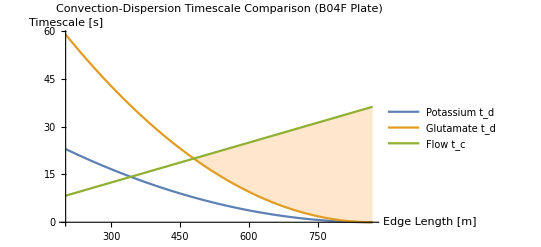

Biofilm Sizes in B04F Before Dispersive Coupling Begins (T=30C)

Potassium~Convection L=342.167 [um]

Glutamate~Convection L=479.739 [um]

```mathematica
ClearAll["Global`*"];
(*Calculations based off of Bae et al. 2009*)
Dp0= 1.98*10^-9 *10^12; (*30C potassium diffusion constant [um^2/s](Friedman 1955)*)
Dg0 = 7.72 * 10^-10*10^12;(*30C Glutamate diffusion constant [um^2/s](Rusakov 2011)*)
u=24; (*Flow velocity [um/s]*)
amax=1.34*10^3; (*Max separation between nearest trap edges [um]*)
lmin=200; (*Minimum trap edge length [um]*)
lmax=amax/2+lmin; (*Maximum trap edge length [um]*)
a[l_]=amax-2*(l-lmin);
td[l_,D0_]=a[l]^2/(4*π^2*D0);
tc[l_]=l/u;
Plot[{td[l,Dp0],td[l,Dg0],tc[l]},{l,lmin,lmax},PlotRange->All,PlotLabel->"Convection-Dispersion Timescale Comparison (B04F Plate)",PlotLegends->{"Potassium t_d","Glutamate t_d","Flow t_c"},AxesLabel->{"Edge Length [m]","Timescale [s]"},Filling->{2->{{3},{LightOrange,White}}}]
lsolp =FullSimplify[Solve[td[l,Dp0]==tc[l],l]][[1]];
lsolg =FullSimplify[Solve[td[l,Dg0]==tc[l],l]][[1]];
Print["Biofilm Sizes in B04F Before Dispersive Coupling Begins (T=30C)"]
Print["Potassium~Convection L=",l/.lsolp, " [um]"]
Print["Glutamate~Convection L=",l/.lsolg, " [um]"]
```

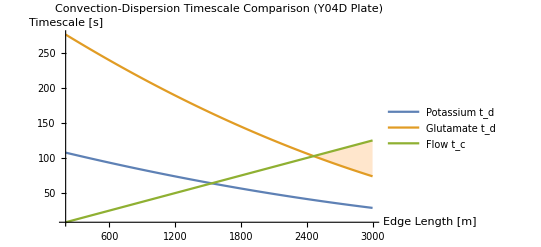

{l→1532.2}

{l→2462.95}

Biofilm Sizes in Y04D Before Dispersive Coupling Begins (T=30C)

Potassium~Convection L=1532.2 [um]

Glutamate~Convection L=2462.95 [um]

```mathematica
ClearAll["Global`*"];
(*Calculations based off of Bae et al. 2009*)
Dp0= 1.98*10^-9 *10^12; (*30C potassium diffusion constant [um^2/s](Friedman 1955)*)
Dg0 = 7.72 * 10^-10*10^12;(*30C Glutamate diffusion constant [um^2/s](Rusakov 2011)*)
u=24; (*Flow velocity [um/s]*)
amax=3*10^3; (*Max separation between nearest trap edges [um]*)
lmin=200; (*Minimum trap radius length [um]*)
lmax=amax; (*Maximum trap edge length [um]*)
a[l_]=amax-(l/2);
td[l_,D0_]=a[l]^2/(4*π^2*D0);
tc[l_]=l/u;
Plot[{td[l,Dp0],td[l,Dg0],tc[l]},{l,lmin,lmax},PlotRange->All,PlotLabel->"Convection-Dispersion Timescale Comparison (Y04D Plate)",PlotLegends->{"Potassium t_d","Glutamate t_d","Flow t_c"},AxesLabel->{"Edge Length [m]","Timescale [s]"},Filling->{2->{{3},{LightOrange,White}}}]
lsolp =FullSimplify[Solve[td[l,Dp0]==tc[l],l]][[1]]
lsolg =FullSimplify[Solve[td[l,Dg0]==tc[l],l]][[1]]
Print["Biofilm Sizes in Y04D Before Dispersive Coupling Begins (T=30C)"]
Print["Potassium~Convection L=",l/.lsolp, " [um]"]
Print["Glutamate~Convection L=",l/.lsolg, " [um]"]
```